```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

#### Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B, PL->-1,bNum->odd, etav->9}],{bL,bT,data}]//Union
```

{{-8,-2,⟨-320(920) × 10⟩_(RowBox[{)},{-8,2,⟨-0.00217(79)⟩_(RowBox[{)},{-6,-3,⟨-560(650) × 10⟩_(RowBox[{)},{-6,3,⟨-380(590) × 10⟩_(RowBox[{)},{-5,-5,⟨-270(320) × 10⟩_(RowBox[{)},{-5,5,⟨570(300) × 10⟩_(RowBox[{)},{-4,-4,⟨-0.00006 ± 0.00042⟩_(RowBox[{)},{-4,-2,⟨0.0014(11)⟩_(RowBox[{)},{-4,-1,⟨0.0032(22)⟩_(RowBox[{)},{-4,1,⟨-0.0007 ± 0.0021⟩_(RowBox[{)},{-4,2,⟨0.0002 ± 0.001⟩_(RowBox[{)},{-4,4,⟨160(440) × 10⟩_(RowBox[{)},{-3,-6,⟨-220(280) × 10⟩_(RowBox[{)},{-3,-3,⟨440(650) × 10⟩_(RowBox[{)},{-3,3,⟨0.00102(66)⟩_(RowBox[{)},{-3,6,⟨560(270) × 10⟩_(RowBox[{)},{-2,-4,⟨140(500) × 10⟩_(RowBox[{)},{-2,-2,⟨-0.0004 ± 0.0011⟩_(RowBox[{)},{-2,-1,⟨0.0011(27)⟩_(RowBox[{)},{-2,1,⟨0.0022(28)⟩_(RowBox[{)},{-2,2,⟨0.0029(12)⟩_(RowBox[{)},{-2,4,⟨260(480) × 10⟩_(RowBox[{)},{-1,-2,⟨-0.0013(11)⟩_(RowBox[{)},{-1,-1,⟨-0.0027(30)⟩_(RowBox[{)},{-1,1,⟨0.0048(30)⟩_(RowBox[{)},{-1,2,⟨0.0018(10)⟩_(RowBox[{)},{0,-7,⟨0 ± 0.⟩_(RowBox[{)},{0,-6,⟨0 ± 0.⟩_(RowBox[{)},{0,-5,⟨0 ± 0.⟩_(RowBox[{)},{0,-4,⟨0 ± 0.⟩_(RowBox[{)},{0,-3,⟨0 ± 0.⟩_(RowBox[{)},{0,-2,⟨0 ± 0.⟩_(RowBox[{)},{0,-1,⟨0 ± 0.⟩_(RowBox[{)},{0,1,⟨0 ± 0.⟩_(RowBox[{)},{0,2,⟨0 ± 0.⟩_(RowBox[{)},{0,3,⟨0 ± 0.⟩_(RowBox[{)},{0,4,⟨0 ± 0.⟩_(RowBox[{)},{0,5,⟨0 ± 0.⟩_(RowBox[{)},{0,6,⟨0 ± 0.⟩_(RowBox[{)},{0,7,⟨0 ± 0.⟩_(RowBox[{)},{1,-2,⟨0.0013(11)⟩_(RowBox[{)},{1,-1,⟨0.0027(30)⟩_(RowBox[{)},{1,1,⟨-0.0048(30)⟩_(RowBox[{)},{1,2,⟨-0.0018(10)⟩_(RowBox[{)},{2,-4,⟨-140(500) × 10⟩_(RowBox[{)},{2,-2,⟨0.0004 ± 0.0011⟩_(RowBox[{)},{2,-1,⟨-0.0011(27)⟩_(RowBox[{)},{2,1,⟨-0.0022(28)⟩_(RowBox[{)},{2,2,⟨-0.0029(12)⟩_(RowBox[{)},{2,4,⟨-260(480) × 10⟩_(RowBox[{)},{3,-6,⟨220(280) × 10⟩_(RowBox[{)},{3,-3,⟨-440(650) × 10⟩_(RowBox[{)},{3,3,⟨-0.00102(66)⟩_(RowBox[{)},{3,6,⟨-560(270) × 10⟩_(RowBox[{)},{4,-4,⟨0.00006 ± 0.00042⟩_(RowBox[{)},{4,-2,⟨-0.0014(11)⟩_(RowBox[{)},{4,-1,⟨-0.0032(22)⟩_(RowBox[{)},{4,1,⟨0.0007 ± 0.0021⟩_(RowBox[{)},{4,2,⟨-0.0002 ± 0.001⟩_(RowBox[{)},{4,4,⟨-160(440) × 10⟩_(RowBox[{)},{5,-5,⟨270(320) × 10⟩_(RowBox[{)},{5,5,⟨-570(300) × 10⟩_(RowBox[{)},{6,-3,⟨560(650) × 10⟩_(RowBox[{)},{6,3,⟨380(590) × 10⟩_(RowBox[{)},{8,-2,⟨320(920) × 10⟩_(RowBox[{)},{8,2,⟨0.00217(79)⟩_(RowBox[{)}}

```mathematica
(*2. Helper to extract list from Jackknife object*)
GiveListfromJK[JK_]:=Module[{},Return[JK/. JacknifeSamples->List]];

(*3. Parameters*)
targetPL=-4;
targetA=A12B;
targetbNum=odd;(*Assuming odd based on your snippet,adjust if needed*)(*Initialize an empty list to store all formatted rows*)exportData={};

(*4. Loop through etav from 0 to 10*)
For[etaVal=0,etaVal<=10,etaVal++,(*Query the database for the current eta*)queryResult=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->targetA,PL->targetPL,bNum->targetbNum,etav->etaVal}],{etav,bL,bT,data}]//Union;
(*Process each resulting row*)For[i=1,i<=Length[queryResult],i++,row=queryResult[[i]];
cEta=row[[1]];
cbL=row[[2]];
cbT=row[[3]];
jkData=row[[4]];
(*Extract samples and take the Imaginary part for ImA12B*)samplesList=GiveListfromJK[jkData];
(*Flatten into a single list:{eta,bL,bT,s1,s2,...,sN}*)flatRow=Join[{cEta,cbL,cbT},samplesList];
(*Append to main data table*)AppendTo[exportData,flatRow];];];

(*5. Export to HDF5*)
(*Note:Adjust the export path to match your remote or local directory structure*)
exportPath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/ImA12B_PL-4__jackknife_data.h5";

(*Exporting as "Dataset1" to match your Python code's f["Dataset1"][:] call*)
Export[exportPath,{"Dataset1"->exportData},"HDF5"];
Print["Exported ImA12B data to: ",exportPath];
```

Exported ImA12B data to: /Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/ImA12B_PL-4_jackknife_data.h5

```mathematica
GiveListfromJK[JK_]:=Module[{},
Return[JK/. JacknifeSamples->List]];

(*Define the PL values you want to extract*)
plValues={-4,-3,-2,-1};

(*Loop over PL values to build a list of rules for the HDF5 Export*)
h5DataRules=Map[With[{pl=#},(*Retrieve the mass entry for this specific PL*)massEntry=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->pl}],{MN}]//Union;
(*Extract the numerical list*)massList=GiveListfromJK[massEntry[[1,1]]];
(*Create a rule formatted as "PL_-4"->{0.616...,0.616...,...}*)"PL_"<>ToString[pl]->massList]&,plValues];

(*Export the rules to a single HDF5 file*)
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/MassN_Jackknife.h5",h5DataRules,"HDF5"];

Print["Successfully saved Mass Jackknife samples to MassN_Jackknife.h5"];
```

Successfully saved Mass Jackknife samples to MassN_Jackknife.h5

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/MassN_Jackknife.h5","StructureGraph"]
```

-Graphics-

```mathematica
MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL, zta}]//Union
```

{{-4,⟨0.786(34)⟩_(RowBox[{)},{-3,⟨0.540(12)⟩_(RowBox[{)},{-2,⟨0.2944(36)⟩_(RowBox[{)},{-1,⟨0.09077(75)⟩_(RowBox[{)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
Return[jackknifeResults];
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
Return[meanvalue];
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
Return[errorvalue];
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,n, k,chisquare,observed,expected,chisquareperDoF,AICvalue, AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
n=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,n}]];
k =Length[para];
chisquareperDoF=chisquare/(n-k);
AICvalue = (2*k)+chisquare;
AICcvalue =AICvalue +((2*k*(k+1))/(n-k-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,nn, kk,chisquare,observed,expected,chisquareperDoF,AICvalue,AICcvalue},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[i_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,i]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d,nparam>1},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[jj],{jj,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
nn=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,nn}]];
kk =Length[para];
chisquareperDoF=chisquare/(nn-kk);
AICvalue = (2*kk)+chisquare;
AICcvalue =AICvalue +((2*kk*(kk+1))/(nn-kk-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

GetChisqfrompara[nxyJKf_,model_,jackknifeResults_,modelFnName_]:=Module[{numFs,fitParamsForFj,fitParamsList,nn, kk,chisquare,observed,expected,chisquareperDoF,AICvalue,AICcvalue},numFs=Length[nxyJKf[[1,4]]];

nn=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,nn}]];
kk =Length[jackknifeResults];
chisquareperDoF=chisquare/(nn-kk);
AICvalue = (2*kk)+chisquare;
AICcvalue =AICvalue +((2*kk*(kk+1))/(nn-kk-1));
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF, AIC->AICvalue,AICc->AICcvalue}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex3para[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
ExpJackk[b_,eta_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=Exp[b[[j]]*eta];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
NFourierTransformJK[model_,fitParams_, xmin_, xmax_]:=Module[{numJK,numParams,NIntegratevaluej,integralValues,jackknifeResult},numJK=Length[fitParams[[1]]];
numParams=Length[fitParams];
NIntegratevaluej[j_]:=Module[{datafitParams},
datafitParams=Table[fitParams[[p,j]],{p,numParams}];
NIntegrate[model[x,datafitParams],{x,xmin, xmax}]];
integralValues=Table[NIntegratevaluej[j],{j,numJK}];
jackknifeResult=JacknifeSamples@@(integralValues);
jackknifeResult];
```

```mathematica
PrintxA2B[ParaFitReA2B_, P1_, b2_]:=Module[{LenPara,fourieReA2Bxforplot, fourierREA2Bforx, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, fourierImA2B, PlotfourieReA2Bx},
LenPara = Length[ParaFitReA2B];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]]/P1 ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[LenPara]];
(*jReA2B =II*2;*)

fourierImA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(1/4 (-3-2 j)) d^-j x Abs[x]^(-(3/2)+j) BesselK[3/2-j,Sqrt[d/c] Abs[x]])/Gamma[j];

fourieReA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierImA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
,{x,-1,1, 0.005}];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[ReA2B]"}, Frame->True , PlotRange->{Full,Full}];
Return[PlotfourieReA2Bx];
];


FitetarangeListImA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKImA2B,modelfitImA2B,dataforfitImA2B,results={},ParaFitImA2B,fitParasImA2B},
dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*0.4959230976723029, 0.5189237816058203, 0.4819451578994735 *)
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*0.4959230976723029]})&/@dataforfitImA2B ;


modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a*x2/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,0.100},{c,0.43},{d,0.094},{k1,-5.83},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{modelfitImA2B[,,,{a,c, d,k1,k2,j}],OutputForm[TableForm[Partition[{"a","c","d","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[fitParasImA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKImA2B],OutputForm[AIC/.fitJKImA2B],PrintxA2B[fitParasImA2B, momL, 9]}];

Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF","AIC","FT Plot ()"}},TableSpacing->{1,2}]];]
```

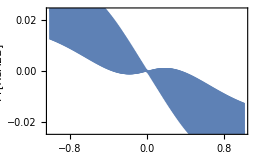
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j | ⟨0.100(40)⟩_(2902J)     ⟨0.16(34)⟩_(2902J)
⟨0.009 ± 0.021⟩_(2902J) ⟨-6.45(19)⟩_(2902J)
⟨-5.085(83)⟩_(2902J)    ⟨1.9(28)⟩_(2902J) | 0.930446 | 215.768 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

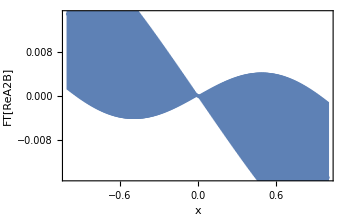
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j | ⟨0.075(43)⟩_(2902J)      ⟨-0.14(32)⟩_(2902J)
⟨-0.008 ± 0.015⟩_(2902J) ⟨-6.59(22)⟩_(2902J)
⟨-5.13(11)⟩_(2902J)      ⟨-780(190)⟩_(2902J) | 0.672499 | 159.277 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

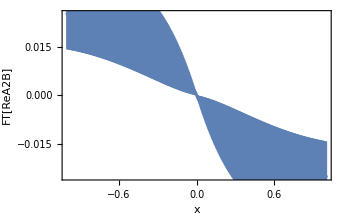
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
(a b_L)/((1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^2) | a  c
d  k1
k2 | ⟨0.201(51)⟩_(2902J)  ⟨1.01(43)⟩_(2902J)
⟨0.066(15)⟩_(2902J)  ⟨-6.48(19)⟩_(2902J)
⟨-5.089(82)⟩_(2902J) | 0.756918 | 176.522 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

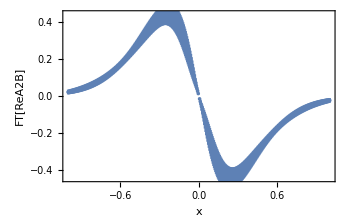
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a b_L (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j | a c
d k1
j | ⟨0.106(33)⟩_(2902J) ⟨0.012(18)⟩_(2902J)
⟨0.012(18)⟩_(2902J) ⟨6.01(75)⟩_(2902J)
⟨2.2(23)⟩_(2902J) | 0.817708 | 189.896 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

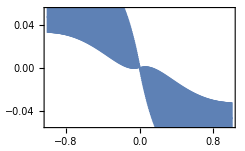
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
(a b_L)/((1+(d+c (1+5.83/η-4.86/(√η))) b_L^2+d b_T^2)^2) | a c
d | ⟨0.197(48)⟩_(2902J) ⟨0.43(21)⟩_(2902J)
⟨0.070(13)⟩_(2902J) |           7
7.18959 10 |           10
1.59609 10 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

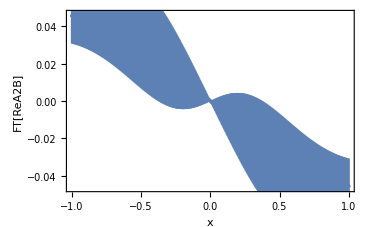
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a b_L (1+(d+c (1+5.83/η-4.86/(√η))) b_L^2+d b_T^2)^-j | a c
d j | ⟨0.092(31)⟩_(2902J)     ⟨0.05 ± 0.12⟩_(2902J)
⟨0.004 ± 0.017⟩_(2902J) ⟨-0.3 ± 5.6⟩_(2902J) | 0.771694 | 178.544 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

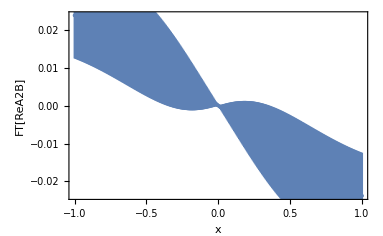
Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot ()
a b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j | ⟨0.100(40)⟩_(2902J)     ⟨0.16(34)⟩_(2902J)
⟨0.009 ± 0.021⟩_(2902J) ⟨-6.45(19)⟩_(2902J)
⟨-5.085(83)⟩_(2902J)    ⟨1.9(28)⟩_(2902J) | 0.723682 | 170.486 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

-1.0418

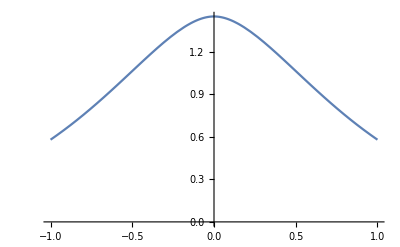

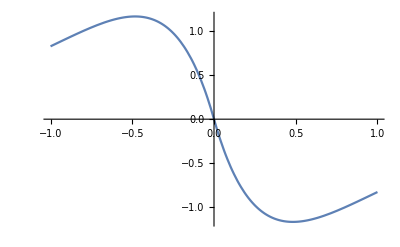

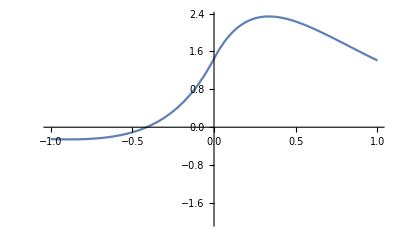

```mathematica
fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];
(*"{⟨4.03(40)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨0.43(17)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨0.094(18)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨-5.83(30)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨-4.86(12)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨2.06(14)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)}"*)
fourierImA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(1/4 (-3-2 j)) d^-j x Abs[x]^(-(3/2)+j) BesselK[3/2-j,Sqrt[d/c] Abs[x]])/Gamma[j];
(*"{⟨0.100(40)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨0.16(34)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨0.009 ± 0.021\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨-6.45(19)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨-5.085(83)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\), ⟨1.9(28)\!\(\*SubscriptBox[\"⟩\", \"2902J\"]\)}"*)
fourierReA2Bx[x_]:=fourierReA2B[x, {4.03,(1+(0.094*9)),0.43/((-1)^2),2.06}];
(*fourierImA2Bx[x_]:=fourierImA2B[x, {0.100/(-1),(1+(0.099*9)),0.16/((-1)^2),2.06}];*)
(* GetChisqfrompara[nxyJKf_,model_,jackknifeResults_,modelFnName_] *)
(*fourierImA2Bx[x_]:=fourierImA2B[x, {4.03/(-1),(1+(0.094*9)),0.43/((-1)^2),2.06}];*)
fourierImA2Bx[x_]:=fourierImA2B[x, {-4.03,(1+(0.094*9)),0.43/((-1)^2),2}];
fourierImA2B[0.25, {-0.106,1.11,0.012,2.2}]
Plot[fourierReA2Bx[x],{x,-1,1},PlotRange->{0,Automatic}]
Plot[fourierImA2Bx[x],{x,-1,1}]
Plot[fourierReA2Bx[x]-fourierImA2Bx[x],{x,-1,1},PlotRange->{-2,Automatic}]
```

```mathematica
PrintxImA2B[ParaFitReA2B_, P1_, b2_]:=Module[{LenPara,fourieReA2Bxforplot, fourierREA2Bforx, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, fourierImA2B, PlotfourieReA2Bx},
LenPara = Length[ParaFitReA2B];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]]/P1 ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[LenPara-1]];

fourierImA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(1/4 (-3-2 j)) d^-j x Abs[x]^(-(3/2)+j) BesselK[3/2-j,Sqrt[d/c] Abs[x]])/Gamma[j];

fourieReA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierImA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
,{x,-1,1, 0.005}];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[ReA2B]"}, Frame->True , PlotRange->{Full,Full}];
Return[PlotfourieReA2Bx];
];

PrintxReA2B[ParaFitReA2B_, P1_, b2_]:=Module[{LenPara,fourieReA2Bxforplot, fourierREA2Bforx, II, bsqJK, aReA2B, dReA2B, cReA2B, jReA2B, fourierReA2B, PlotfourieReA2Bx},
LenPara = Length[ParaFitReA2B];
II = ParaFitReA2B[[1]] /ParaFitReA2B[[1]] ;
aReA2B = ParaFitReA2B[[1]] ;
dReA2B=II+ParaFitReA2B[[3]]*b2;
cReA2B=(ParaFitReA2B[[2]])/(P1^2);
jReA2B = ParaFitReA2B[[LenPara-1 ]];

fourierReA2B[x_, {a_,d_,c_,j_}] :=(2^(1-j) a (c/d)^(-(1/4)-j/2) d^-j Abs[x]^(-(1/2)+j) BesselK[1/2-j,Abs[x]/Sqrt[c/d]])/Gamma[j];

fourieReA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierReA2B,{aReA2B,dReA2B,cReA2B,jReA2B}, x];
AppendTo[fourieReA2Bxforplot,{x,fourierREA2Bforx}];
,{x,0,1, 0.005}];
PlotfourieReA2Bx= ErrorListPlot[MakeErrBars[fourieReA2Bxforplot],FrameLabel->{ , "FT[ReA2B]"}, Frame->True , PlotRange->{Full,Full}];
Return[PlotfourieReA2Bx];
];

FitetarangeListImA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKImA2B,modelfitImA2B,dataforfitImA2B,results={},ParaFitImA2B,fitParasImA2B,dataforfitReA2B, modelfitReA2B, fitJKReA2B, fitParasReA2B, },
dataforfitReA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
modelfitReA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_,f_}]:=a*Exp[-f*x1]/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKReA2B=JackknifeFit4DGaussianCons[dataforfitReA2B,modelfitReA2B[n,bL,bT,{a,c,d,k1, k2,nparam,f}],{{a,4.01},{c,0.6},{d,0.094},{k1,-5.83},{k2,-4.86},{nparam,2.06},{f,0.5}},{n,bL,bT},modelfitReA2B];
fitParasReA2B=FitParameters/.fitJKReA2B;
AppendTo[results,{"Re ",modelfitReA2B[,,,{a,c, d,k1,k2,j,f}],OutputForm[TableForm[Partition[{"a","c","d","k1","k2","j","f"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[fitParasReA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKReA2B],OutputForm[AIC/.fitJKReA2B],PrintxReA2B[fitParasReA2B, momL, 9]}];

dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_,f_}]:=a*Exp[-f*x1]*x2/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d,k1, k2,nparam,f}],{{a,0.100},{c,0.43},{d,0.094},{k1,-5.83},{k2,-4.86},{nparam,2.06},{f,0.5}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{"Im ",modelfitImA2B[,,,{a,c, d,k1,k2,j,f}],OutputForm[TableForm[Partition[{"a","c","d","k1","k2","j","f"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[fitParasImA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKImA2B],OutputForm[AIC/.fitJKImA2B],PrintxImA2B[fitParasImA2B, momL, 9]}];
Print["Gaussian-type fit for  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Amplitude","Model Expression","Params List","Fitted Values","/DoF","AIC","FT Plot (* ; )"}},TableSpacing->{1,2}]];]
```

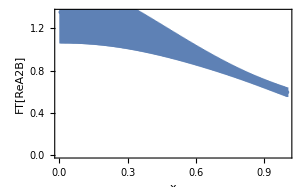
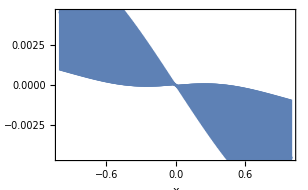
Gaussian-type fit for  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Amplitude | Model Expression | Params List | Fitted Values | /DoF | AIC | FT Plot (* ; )
Re  | a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j
f | ⟨4.01(58)⟩_(2902J)  ⟨0.43(17)⟩_(2902J)
⟨0.094(18)⟩_(2902J) ⟨-5.81(33)⟩_(2902J)
⟨-4.86(14)⟩_(2902J) ⟨2.06(14)⟩_(2902J)
⟨0.496(12)⟩_(2902J) | 1.56911 | 356.065 | -Graphics-
Im  | a ⅇ^(-f η) b_L (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j | a  c
d  k1
k2 j
f | ⟨0.037(19)⟩_(2902J)    ⟨0.24(37)⟩_(2902J)
⟨0.01 ± 0.013⟩_(2902J) ⟨-6.00(24)⟩_(2902J)
⟨-4.91(11)⟩_(2902J)    ⟨2.3(34)⟩_(2902J)
⟨0.352(64)⟩_(2902J) | 0.659107 | 157.685 | -Graphics-

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

```mathematica
GiveListfromJK[JK_]:=Module[{},
Return[JK/. JacknifeSamples->List]];
etabLbTdata = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-1, bNum->even}],{etav, bL, bT,data}];
Length[etabLbTdata]
etabLbTdata[[10]]
etabLbTdata[[10]][[4]]
Length[etabLbTdata[[1]][[4]]]
GiveListfromJK[InputForm[etabLbTdata[[10]][[4]]]];
```

726

{0,0,-2,⟨0.5098(30)⟩_(RowBox[{)}

⟨0.5098(30)⟩_(RowBox[{)

2903

```mathematica
(*1. Extract kinematics (first 3 columns)*)kinematics=etabLbTdata[[All,1;;3]];

(*2. Force conversion of the 4th column.Apply (@@) strips the JacknifeSamples wrapper and leaves only the numbers*)
samples=Map[List@@#&,etabLbTdata[[All,4]]];

(*3. CRITICAL CHECK:Make sure we have perfect 2D grids of numbers*)
Print["Kinematics shape: ",Dimensions[kinematics]];
Print["Samples shape: ",Dimensions[samples]];

(*4. Export using an Association (the most reliable HDF5 method in Mathematica)*)
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/A2B_jackknife_data.h5",<|"etabLbT"->kinematics,"data"->samples|>]
```

Kinematics shape: {726,3}

Samples shape: {726,2903}

/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/A2B_jackknife_data.h5

```mathematica
mom =-4;
etabLbTdata = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->mom, bNum->even}],{etav, bL, bT,data}];
cleanData=Map[Flatten,etabLbTdata/. JacknifeSamples->List];
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/ImA2B_PL" <> ToString[mom] <> "_jackknife___data.h5",cleanData]
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/ImA2B_PL-4_jackknife_data.h5

```mathematica
(*PlotAbLfordiffbLbT[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
(*bTlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bT]];
bLlist= Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bL]];*)
rawData=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bL,bT}];
Print[rawData//Sort];
filteredData=Select[rawData,(#[[1]]^2+#[[2]]^2)>=0^2&];
Print[filteredData//Sort];
bLlist=Union[filteredData[[All,1]]];
bTlist=Union[filteredData[[All,2]]];
Print[bLlist];
Print[bTlist];
PlotbLforDiffbTList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi, bNum->bnum}],{bL,data}];
bLAmp=Select[bLAmp,MemberQ[bLlist,#[[1]]]&];
AppendTo[PlotbLforDiffbTList,bLAmp];
 ,{bTi,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi, Length[bTlist]}],FrameLabel->{, Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bL_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbL,"PDF",ImageResolution->600];
PlotbTforDiffbLList={};
Do[
bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi, bNum->bnum}],{bT,data}];
bLAmp=Select[bLAmp,MemberQ[bTlist,#[[1]]]&];
AppendTo[PlotbTforDiffbLList,bLAmp];
 ,{bLi,bLlist}];
PlotbT= ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi, Length[bLlist]}],FrameLabel->{,ampname b bnum}, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}], ImageSize->450];
Export["/Users/hariprashadravikumar/Downloads/bT_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotbT,"PDF",ImageResolution->600];GraphicsRow[{PlotbL,PlotbT},ImageSize->Full]
)*)
modelfitReA2B[x1_,x2_,x3_]:=0.153*x2*Exp[-0.4959230976723029*x1]/(1+(0.0345+0.0345)*x2^2+0.0345*x3^2)^2;
(*modelfitReA2B[x1_,x2_,x3_]:=4.03*Exp[-0.4959230976723029*x1]/(1+(0.094+0.43(1+5.83/x1-4.86/Sqrt[x1]))*x2^2+0.094*x3^2)^2.06;*)
modelfitReA2BPbbsq[x1_,x2_,x3_]:=0.153*x2*Exp[-0.4959230976723029*x1]/(1+(0.0345)*x2^2+0.0345*x3)^2;

PlotAbLfordiffbLbT[ampname_,P1_,etavalue_,bnum_,Nnum_]:=(Print[Nnum ampname," => PL = ",P1," ,eta = ",etavalue];
rawData=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bL,bT}];
(*Filter pairs satisfying the radius condition*)filteredPairs=Select[rawData,Sqrt[#[[1]]^2+#[[2]]^2]>=3&&#[[1]]!=0&];

bLlist=Union[filteredPairs[[All,1]]];
bTlist=Union[filteredPairs[[All,2]]];

(*Convert to a lookup set for fast pair membership testing*)validPairSet=Association[Rule[#,True]&/@filteredPairs];
(*---Plot vs bL (curves for different bT)---*)PlotbLforDiffbTList={};
Do[bLAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bT->bTi,bNum->bnum}],{bL,data}];
bLAmp =({#[[1]],#[[2]]/modelfitReA2B[etavalue,#[[1]],bTi]})&/@bLAmp ;
(*Keep only pairs {bL,bTi} that passed the radius filter*)bLAmp=Select[bLAmp,KeyExistsQ[validPairSet,{#[[1]],bTi}]&];
AppendTo[PlotbLforDiffbTList,bLAmp];,{bTi,bTlist}];
PlotbL=ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bTi]]],{bTi,Length[bTlist]}],FrameLabel->{Subscript[b,L],Nnum ampname},Frame->True,PlotRange->Full,PlotLegends->Table["bT = "<>ToString[bTlist[[bTi]]],{bTi,Length[bTlist]}],ImageSize->450];
(*---Plot vs bT (curves for different bL)---*)PlotbTforDiffbLList={};
Do[bTAmp=MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->ampname,PL->P1,etav->etavalue,bL->bLi,bNum->bnum}],{bT,data}];
bTAmp =({#[[1]],#[[2]]/modelfitReA2B[etavalue,bLi,#[[1]]]})&/@bTAmp ;
(*Keep only pairs {bLi,bT} that passed the radius filter*)bTAmp=Select[bTAmp,KeyExistsQ[validPairSet,{bLi,#[[1]]}]&];
AppendTo[PlotbTforDiffbLList,bTAmp];,{bLi,bLlist}];
PlotbT=ErrorListPlot[Table[MakeErrBars[PlotbTforDiffbLList[[bLi]]],{bLi,Length[bLlist]}],FrameLabel->{Subscript[b,T],ampname b bnum},Frame->True,PlotRange->Full,PlotLegends->Table["bL = "<>ToString[bLlist[[bLi]]],{bLi,Length[bLlist]}],ImageSize->450];
GraphicsRow[{PlotbL,PlotbT},ImageSize->Full])
PlotAfordiffBPbbsq[ampname_,P1_, etavalue_, bnum_, Nnum_]:=(
Print[Nnum ampname," =>  = ",P1," ,eta = ", etavalue];
(*bsquarelist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],bsquare]];
bsquarelist = Select[bsquarelist,9<=#&];
Pb32by2Pilist= Union[MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue, bNum->bnum}],Pb32by2Pi]];
Pb32by2Pilist = Select[Pb32by2Pilist,#<=-3&&#>=3&];*)

rawData=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bNum->bnum}],{bsquare,Pb32by2Pi}];
filteredData=Select[rawData,#[[1]]>=9&&#[[2]]!=0&];
bsquarelist=Union[filteredData[[All,1]]];
Pb32by2Pilist=Union[filteredData[[All,2]]];
PlotPbforDiffbsq={};
Do[
PbAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,bsquare->bsqi, bNum->bnum}],{Pb32by2Pi,data}];
PbAmp =({#[[1]],#[[2]]/-modelfitReA2BPbbsq[etavalue,#[[1]],bsqi]})&/@PbAmp ;
AppendTo[PlotPbforDiffbsq,PbAmp];
 ,{bsqi,bsquarelist}];
PlotbP= ErrorListPlot[Table[MakeErrBars[PlotPbforDiffbsq[[bsqi]]],{bsqi, Length[bsquarelist]}],FrameLabel->{ , Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[bsquarelist[[bsqi]]],{bsqi,Length[bsquarelist]}], ImageSize->450];
PlotbsqforDiffPb={};
Do[
bsqAmp=MemDBGet[AmpDBPbbsq,MemDBSelect[AmpDBPbbsq,{A->ampname,PL->P1,etav->etavalue,Pb32by2Pi->Pbi, bNum->bnum}],{bsquare,data}];
bsqAmp=Select[bsqAmp,#[[1]]>=9&];
bsqAmp =({#[[1]],#[[2]]/modelfitReA2BPbbsq[etavalue,Pbi,#[[1]]]})&/@bsqAmp ;
AppendTo[PlotbsqforDiffPb,bsqAmp];
 ,{Pbi,Pb32by2Pilist}];
Plotbsq= ErrorListPlot[Table[MakeErrBars[PlotbsqforDiffPb[[Pbi]]],{Pbi, Length[Pb32by2Pilist]}],FrameLabel->{,Nnum ampname }, Frame->True ,PlotRange->Full,PlotLegends->Table[" = "<>ToString[Pb32by2Pilist[[Pbi]]],{Pbi,Length[Pb32by2Pilist]}], ImageSize->450];
(*Export["/Users/hariprashadravikumar/Downloads/bsq_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotbsq,"PDF",ImageResolution->600];*)
GraphicsRow[{PlotbP,Plotbsq},ImageSize->Full]
)
```

```mathematica
PlotAbLfordiffbLbT[A12B,-1,0, odd, "Im"]
PlotAfordiffBPbbsq[A12B,-1,0, odd, "Im"]
```

Im A12B => PL = -1 ,eta = 0

-Graphics-

Im A12B =>  = -1 ,eta = 0

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A12B,-1,6, odd, "Im"]
PlotAfordiffBPbbsq[A12B,-1,6, odd, "Im"]
```

Im A12B => PL = -1 ,eta = 6

-Graphics-

Im A12B =>  = -1 ,eta = 6

-Graphics-

```mathematica
PlotAbLfordiffbLbT[A2B,-1,8, even, "Re"](*A2B Re divided by model a ⅇ^(-f η) (1+(d+c (1-k1/η+k2/(√η))) Subscript[b, L]^2+d Subscript[b, T]^2)^-j*)
```

Re A2B => PL = -1 ,eta = 8

-Graphics-

```mathematica
Sqrt[1/(2Pi)]*Integrate[a*Tanh[g*Pb]/(d+c*Pb^2)^j*Sin[Pb*x],{Pb,-Infinity,Infinity},Assumptions->{a>0,c>0,d>0,x∈Reals}]
```

Integrate[a (d+c Pb^2)^-j Sin[Pb x] Tanh[g Pb],{Pb,-∞,∞},Assumptions→{a>0,c>0,d>0,x∈ℝ}]/(√(2 π))

```mathematica
expr=a*Tanh[g*Pb]/(d+c*Pb^2)^j;
sol=FourierTransform[expr,Pb,x,Assumptions->{a>0,c>0,d>0,j>1/2,x∈Reals}]
```

FourierTransform[a (d+c Pb^2)^-j Tanh[g Pb],Pb,x,Assumptions→{a>0,c>0,d>0,j>1/2,x∈ℝ}]

```mathematica
FitetarangeListImA2B[bminForFit_,momL_,etamin_,etamax_]:=Module[{fitJKImA2B,modelfitImA2B,dataforfitImA2B,results={},ParaFitImA2B,fitParasImA2B},
dataforfitImA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->odd}],{etav, bL, bT,data}],#[[1]]>=etamin&&#[[1]]<=etamax&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
(*0.4959230976723029, 0.5189237816058203, 0.4819451578994735 *)
dataforfitImA2B =({#[[1]],#[[2]],#[[3]],#[[4]]/Exp[-#[[1]]*0.4959230976723029]})&/@dataforfitImA2B ;


modelfitImA2B[x1_,x2_,x3_,{a_,c_,d_,k1_,k2_,j_}]:=a*Tanh[0.2*x2]/(1+(d+c*(1-k1/x1+k2/Sqrt[x1]))*x2^2+d*x3^2)^j;
fitJKImA2B=JackknifeFit4DGaussianCons[dataforfitImA2B,modelfitImA2B[n,bL,bT,{a,c,d,k1, k2,nparam}],{{a,0.100},{c,0.43},{d,0.094},{k1,-5.83},{k2,-4.86},{nparam,2.06}},{n,bL,bT},modelfitImA2B];
fitParasImA2B=FitParameters/.fitJKImA2B;
AppendTo[results,{modelfitImA2B[,,,{a,c, d,k1,k2,j}],OutputForm[TableForm[Partition[{"a","c","d","k1","k2","j"},2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[TableForm[Partition[fitParasImA2B,2,2,{1,1},{}],TableSpacing->{0,1}]],OutputForm[chisquareDoF/.fitJKImA2B],OutputForm[AIC/.fitJKImA2B]}];

Print["Gaussian-type fit for Re  for =",momL,"\n","",bminForFit," are SELECTED for fit!\n",etamin,"",etamax," are SELECTED for fit!\n \n",TableForm[results,TableHeadings->{None,{"Model Expression","Params List","Fitted Values","/DoF"}},TableSpacing->{1,2}]];]
```

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j Tanh[0.2 b_L] | a  c
d  k1
k2 j | ⟨0.49(19)⟩_(2902J)      ⟨0.14(44)⟩_(2902J)
⟨0.006 ± 0.029⟩_(2902J) ⟨-6.53(20)⟩_(2902J)
⟨-5.146(88)⟩_(2902J)    ⟨1. ± 2.8⟩_(2902J) | 0.722106 | 170.141

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
a (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j Tanh[0.2 b_L] | a c
d k1
j | ⟨0.53(13)⟩_(2902J)  ⟨0.013(20)⟩_(2902J)
⟨0.013(20)⟩_(2902J) ⟨7.32(64)⟩_(2902J)
⟨1.7(24)⟩_(2902J) | 0.841422 | 195.113

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
a (1+(d+c (1-k1/η)) b_L^2+d b_T^2)^-j Tanh[g b_L] | a  c
d  g
k1 j |                3
⟨-3.00(11) × 10 ⟩_(2902J) ⟨0.011(18)⟩_(2902J)
⟨0.011(18)⟩_(2902J)       ⟨0.1424(52)⟩_(2902J)
⟨6.05(75)⟩_(2902J)        ⟨2.3(23)⟩_(2902J) | 0.821918 | 192.

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j Tanh[g b_L] | a  c
d  g
k1 k2
j | ⟨0.1 ± 0.5⟩_(2902J)  ⟨0.36(44)⟩_(2902J)
⟨0.020(29)⟩_(2902J)  ⟨0.21(18)⟩_(2902J)
⟨-6.55(21)⟩_(2902J)  ⟨-5.16(12)⟩_(2902J)
⟨-0.5 ± 2.8⟩_(2902J) | 0.722939 | 171.601

```mathematica
FitetarangeListImA2B[3,-1,6,10]
```

Gaussian-type fit for Re  for =-1
3 are SELECTED for fit!
610 are SELECTED for fit!
 
Model Expression | Params List | Fitted Values | /DoF | 
a (1+(d+c (1-k1/η+k2/(√η))) b_L^2+d b_T^2)^-j Tanh[g b_L] | a  c
d  g
k1 k2
j | ⟨0.1 ± 0.5⟩_(2902J)  ⟨0.36(44)⟩_(2902J)
⟨0.020(29)⟩_(2902J)  ⟨0.21(18)⟩_(2902J)
⟨-6.55(21)⟩_(2902J)  ⟨-5.16(12)⟩_(2902J)
⟨-0.5 ± 2.8⟩_(2902J) | 0.722939 | 171.601